```mathematica
ΩLine=Ω0(1+σ*ϵ)
ΩStar=(1+3/8*U(-a+b/3+c/Ω0^2))*Ω0
σ[U_]:=PlusMinus[(1+3/8*U(-a+b/3+c/Ω0^2))*Ω0/Ω0-1,1/Ω0^2*Sqrt[f^2/(4U^2)-μ^2*Ω0^2]]
σ1[U_]:=(1+3/8*U(-a+b/3+c/Ω0^2))*Ω0/Ω0-1+1/Ω0^2*Sqrt[f^2/(4U^2)-μ^2*Ω0^2]
σ2[U_]:=(1+3/8*U(-a+b/3+c/Ω0^2))*Ω0/Ω0-1-1/Ω0^2*Sqrt[f^2/(4U^2)-μ^2*Ω0^2]
θ[σ_,U_]:=ArcTan[μ/((1+3/8*U(-a+b/3+c/Ω0^2))*Ω0-(1+σ)*Ω0 )]
σ[U]
θ[σ,U]
```

(1+ϵ σ) Ω0

(1+3/8 U (-a+b/3+c/Ω0^2)) Ω0

3/8 U (-a+b/3+c/Ω0^2)±(√(f^2/(4 U^2)-μ^2 Ω0^2))/Ω0^2

ArcTan[μ/(-(1+σ) Ω0+(1+3/8 U (-a+b/3+c/Ω0^2)) Ω0)]

```mathematica
Ω0=3.652621;
ϵ=1;
μ=0.001;
a=2.143318;
b=4.596773;
c=10.265234;
f=0.0025;
σ[U]
θ[σ,U]
```

(-1+1. (1+0.0593823 U))±0.0749533 √(-0.0000133416+(1.5625×10^-6)/U^2)

ArcTan[0.001/(3.65262 (1+0.0593823 U)-3.65262 (1+σ))]

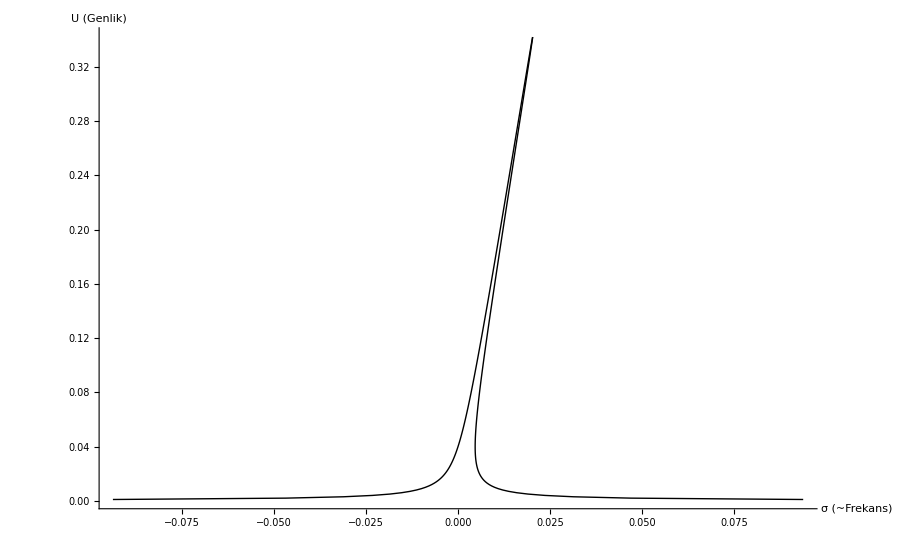

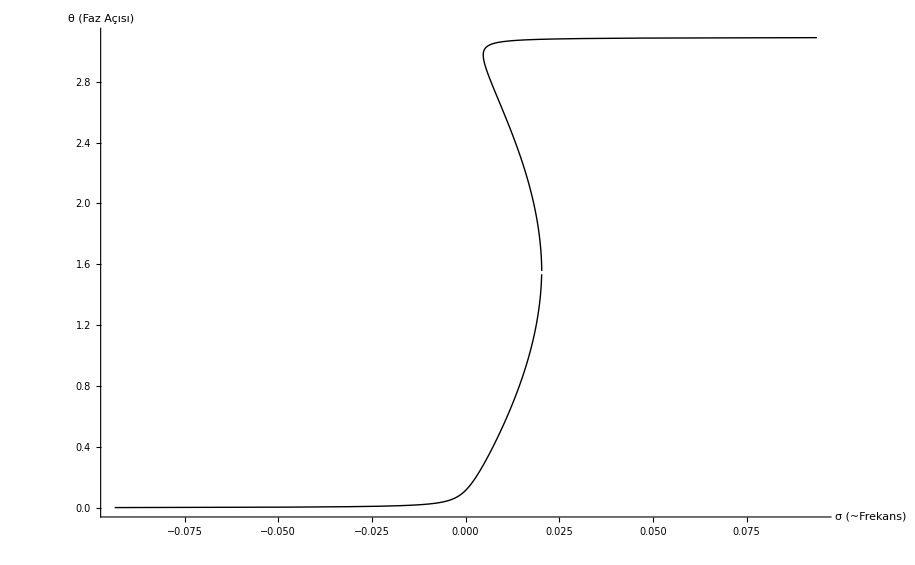

```mathematica
tb3=Table[{σ1[i/1000],θ[σ1[i/1000],i/1000]+Pi-0.05},{i,342}];
tb4=Table[{σ2[i/1000],θ[σ2[i/1000],i/1000]},{i,342}];
tbI=Table[{σ1[i/1000],i/1000},{i,342}];
tbII=Table[{σ2[i/1000],i/1000},{i,342}];
ListPlot[{tbI,tbII},Joined->True,AxesLabel->{"σ (~Frekans)","U (Genlik)"},PlotStyle->{Black,Black,Thickness[1],Thickness[1]}]
ListPlot[{tb3,tb4},Joined->True,AxesLabel->{"σ (~Frekans)","θ (Faz Açısı)"},PlotStyle->{Black,Black,Thickness[1],Thickness[1]}]
```

```mathematica
Grid[{{U,σ1,σ2,θ1,θ2}},Frame->All]
Grid [Table[{N[i/50],σ1[i/50],σ2[i/50],θ[σ1[i/50],i/50]+Pi-0.05,θ[σ2[i/50],i/50]},{i,17
}]
,Frame->All]
```

U | σ1 | σ2 | θ1 | θ2

0.02 | 0.00586422 | -0.00348893 | 3.03312 | 0.0584753
0.04 | 0.00470153 | 0.0000490572 | 2.97444 | 0.117152
0.06 | 0.00510028 | 0.0020256 | 2.91536 | 0.176237
0.08 | 0.00588928 | 0.00361189 | 2.85564 | 0.235951
0.1 | 0.00683426 | 0.00504221 | 2.79506 | 0.296537
0.12 | 0.00785707 | 0.00639469 | 2.73333 | 0.358267
0.14 | 0.00892419 | 0.00770286 | 2.67013 | 0.42146
0.16 | 0.0100188 | 0.00898354 | 2.60509 | 0.486501
0.18 | 0.0111315 | 0.0102461 | 2.53773 | 0.553864
0.2 | 0.0122566 | 0.0114963 | 2.46743 | 0.624164
0.22 | 0.0133903 | 0.0127379 | 2.39336 | 0.698228
0.24 | 0.01453 | 0.0139735 | 2.31437 | 0.777224
0.26 | 0.0156737 | 0.0152051 | 2.22867 | 0.862921
0.28 | 0.0168194 | 0.0164347 | 2.13334 | 0.958251
0.3 | 0.017965 | 0.0176644 | 2.02278 | 1.06881
0.32 | 0.0191061 | 0.0188986 | 1.88313 | 1.20846
0.34 | 0.0202213 | 0.0201587 | 1.63476 | 1.45683

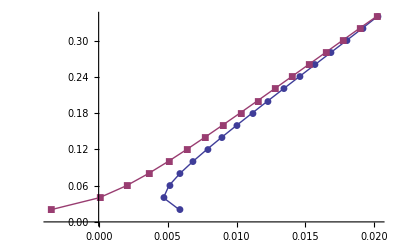

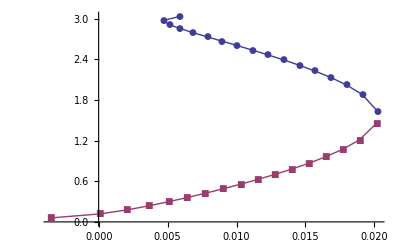

```mathematica
ListPlot[{
Table[{σ1[i/50],N[i/50]},{i,17}],
Table[{σ2[i/50],N[i/50]},{i,17}]
},Joined->True,PlotMarkers->Automatic]
ListPlot[{
tb3=Table[{σ1[i/50],θ[σ1[i/50],i/50]+Pi-0.05},{i,17}],
tb4=Table[{σ2[i/50],θ[σ2[i/50],i/50]},{i,17}]
},Joined->True,PlotMarkers->Automatic]
```

(0.5625+2 Cos[t]) x[t]+0.075 x'[t]+x''[t]==0

{{x[t]→InterpolatingFunction[{{0.,45.}},<>][t],x'[t]→InterpolatingFunction[{{0.,45.}},<>][t]}}

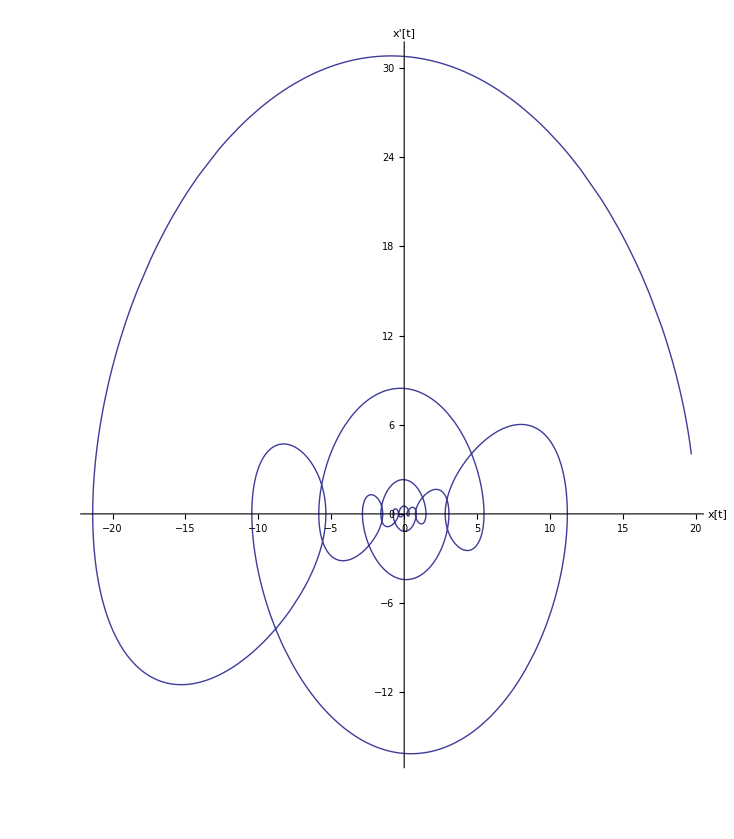

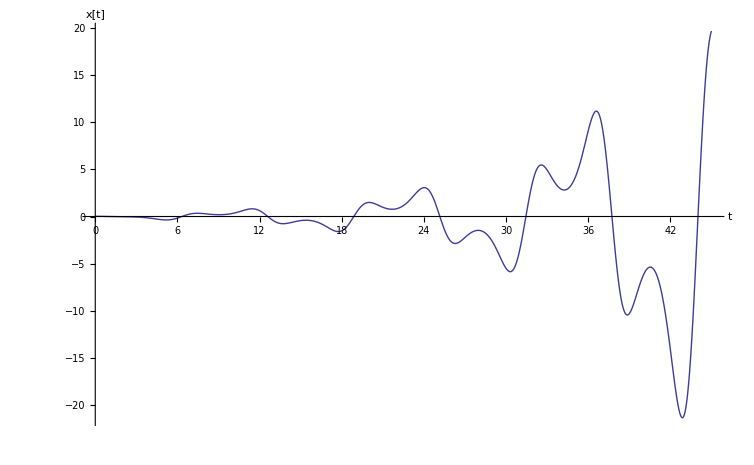

```mathematica
β=0.75;
ϵ=2;
μ=0.05;
x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0
sol=
NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==0.02,x'[0]==0},{x[t],x'[t]},{t,0,45}]
ParametricPlot[Evaluate[{x[t], x'[t]} /.sol], {t,0,45},PlotRange->All,AxesLabel->{"x[t]","x'[t]"}] 
Plot[Evaluate[x[t]/.sol],{t,0,45},PlotRange->All,AxesLabel->{"t","x[t]"}]
```

(0.5625+0.2 Cos[t]) x[t]+0.075 x'[t]+x''[t]==0

{{x[t]→InterpolatingFunction[{{0.,45.}},<>][t],x'[t]→InterpolatingFunction[{{0.,45.}},<>][t]}}

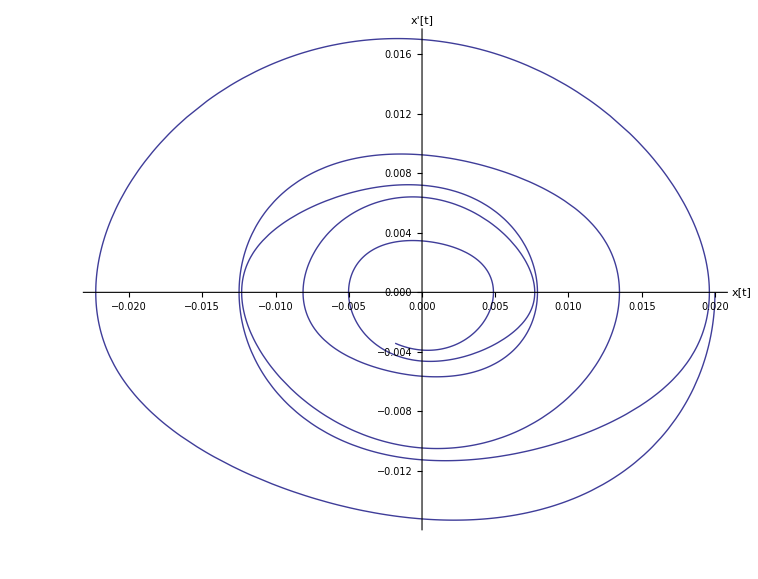

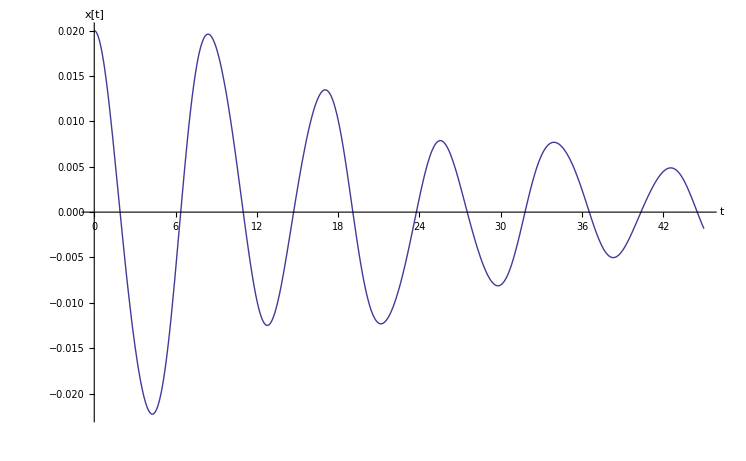

```mathematica
β=0.75;
ϵ=0.2;
μ=0.05;
x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0
sol=
NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==0.02,x'[0]==0},{x[t],x'[t]},{t,0,45}]
ParametricPlot[Evaluate[{x[t], x'[t]} /.sol], {t,0,45},PlotRange->All,AxesLabel->{"x[t]","x'[t]"}] 
Plot[Evaluate[x[t]/.sol],{t,0,45},PlotRange->All,AxesLabel->{"t","x[t]"}]
```